```mathematica
Monitor[Table[With[{g=Graph[ReadGrof[k]]},
With[{sol=First[FindFullFormula4[g]]},
With[
{
edges=EdgeCount[g],
zeroes=Length[Select[Flatten[MyPermute[g,sol]],#==0&]]
},
{k,sol,VertexCount[g],edges,zeroes, zeroes/2}]
]],{k,1,100}],k]//TableForm
```

1 | v1x2x3x4 | 4 | 6 | 0 | 0
2 | v14x2x3x5 | 5 | 9 | 0 | 0
3 | v16x24x3x5 | 6 | 12 | 2 | 1
4 | v1x25x36x4 | 6 | 12 | 2 | 1
5 | v15x24x3x67 | 7 | 15 | 6 | 3
6 | v14x25x37x6 | 7 | 15 | 6 | 3
7 | v1x24x35x67 | 7 | 15 | 6 | 3
8 | v147x26x3x5 | 7 | 15 | 4 | 2
9 | v16x24x3x57 | 7 | 15 | 6 | 3
10 | v15x28x34x67 | 8 | 18 | 12 | 6
11 | v18x24x35x67 | 8 | 18 | 12 | 6
12 | v145x28x3x67 | 8 | 18 | 10 | 5
13 | v15x26x3x478 | 8 | 18 | 10 | 5
14 | v158x2x36x47 | 8 | 18 | 10 | 5
15 | v15x24x38x67 | 8 | 18 | 12 | 6
16 | v158x24x3x67 | 8 | 18 | 10 | 5
17 | v15x24x38x67 | 8 | 18 | 12 | 6
18 | v14x28x35x67 | 8 | 18 | 12 | 6
19 | v14x28x35x67 | 8 | 18 | 12 | 6
20 | v14x25x37x68 | 8 | 18 | 12 | 6
21 | v1x267x35x48 | 8 | 18 | 10 | 5
22 | v178x246x3x5 | 8 | 18 | 8 | 4
23 | v16x24x38x57 | 8 | 18 | 12 | 6
24 | v15x26x34x789 | 9 | 21 | 18 | 9
25 | v159x24x36x78 | 9 | 21 | 18 | 9
26 | v156x2x34x789 | 9 | 21 | 16 | 8
27 | v145x28x39x67 | 9 | 21 | 18 | 9
28 | v15x28x39x467 | 9 | 21 | 18 | 9
29 | v167x28x34x59 | 9 | 21 | 18 | 9
30 | v16x278x349x5 | 9 | 21 | 16 | 8
31 | v149x28x35x67 | 9 | 21 | 18 | 9
32 | v159x28x34x67 | 9 | 21 | 18 | 9
33 | v15x28x349x67 | 9 | 21 | 18 | 9
34 | v15x289x34x67 | 9 | 21 | 18 | 9
35 | v156x24x39x78 | 9 | 21 | 18 | 9
36 | v189x25x34x67 | 9 | 21 | 18 | 9
37 | v1x268x35x479 | 9 | 21 | 16 | 8
38 | v189x24x35x67 | 9 | 21 | 18 | 9
39 | v147x2x35x689 | 9 | 21 | 16 | 8
40 | v1x247x35x689 | 9 | 21 | 16 | 8
41 | v18x249x35x67 | 9 | 21 | 18 | 9
42 | v149x28x35x67 | 9 | 21 | 18 | 9
43 | v189x24x35x67 | 9 | 21 | 18 | 9
44 | v149x28x35x67 | 9 | 21 | 18 | 9
45 | v149x28x35x67 | 9 | 21 | 18 | 9
46 | v168x24x37x59 | 9 | 21 | 18 | 9
47 | v145x26x3x789 | 9 | 21 | 16 | 8
48 | v159x28x3x467 | 9 | 21 | 16 | 8
49 | v18x245x39x67 | 9 | 21 | 18 | 9
50 | v167x28x3x459 | 9 | 21 | 16 | 8
51 | v1459x28x3x67 | 9 | 21 | 14 | 7
52 | v145x28x39x67 | 9 | 21 | 18 | 9
53 | v145x289x3x67 | 9 | 21 | 16 | 8
54 | v15x246x3x789 | 9 | 21 | 16 | 8
55 | v1478x26x3x59 | 9 | 21 | 14 | 7
56 | v148x267x39x5 | 9 | 21 | 16 | 8
57 | v159x26x3x478 | 9 | 21 | 16 | 8
58 | v15x26x39x478 | 9 | 21 | 18 | 9
59 | v15x269x3x478 | 9 | 21 | 16 | 8
60 | v159x26x3x478 | 9 | 21 | 16 | 8
61 | v15x26x39x478 | 9 | 21 | 18 | 9
62 | v1x247x369x58 | 9 | 21 | 16 | 8
63 | v158x2x369x47 | 9 | 21 | 16 | 8
64 | v158x2x36x479 | 9 | 21 | 16 | 8
65 | v149x25x38x67 | 9 | 21 | 18 | 9
66 | v149x25x38x67 | 9 | 21 | 18 | 9
67 | v15x249x38x67 | 9 | 21 | 18 | 9
68 | v159x24x3x678 | 9 | 21 | 16 | 8
69 | v158x24x39x67 | 9 | 21 | 18 | 9
70 | v158x24x39x67 | 9 | 21 | 18 | 9
71 | v158x249x3x67 | 9 | 21 | 16 | 8
72 | v1x246x35x789 | 9 | 21 | 16 | 8
73 | v1469x278x3x5 | 9 | 21 | 12 | 6
74 | v145x26x3ax789 | 10 | 24 | 26 | 13
75 | v15x246x3ax789 | 10 | 24 | 26 | 13
76 | v156x2ax34x789 | 10 | 24 | 26 | 13
77 | v1789x26x34x5a | 10 | 24 | 24 | 12
78 | v189x267x34ax5 | 10 | 24 | 24 | 12
79 | v16x25x34ax789 | 10 | 24 | 26 | 13
80 | v14x26ax35x789 | 10 | 24 | 26 | 13
81 | v15x289x34x67a | 10 | 24 | 26 | 13
82 | v15ax28x349x67 | 10 | 24 | 26 | 13
83 | v15x26x34ax789 | 10 | 24 | 26 | 13
84 | v15x26ax34x789 | 10 | 24 | 26 | 13
85 | v15ax26x34x789 | 10 | 24 | 26 | 13
86 | v15ax26x34x789 | 10 | 24 | 26 | 13
87 | v158x26x34x79a | 10 | 24 | 26 | 13
88 | v156x24x3ax789 | 10 | 24 | 26 | 13
89 | v16x25x34ax789 | 10 | 24 | 26 | 13
90 | v16ax24x35x789 | 10 | 24 | 26 | 13
91 | v14x26ax35x789 | 10 | 24 | 26 | 13
92 | v16ax25x34x789 | 10 | 24 | 26 | 13
93 | v156x2ax34x789 | 10 | 24 | 26 | 13
94 | v18ax25x36x479 | 10 | 24 | 26 | 13
95 | v1459x2ax36x78 | 10 | 24 | 24 | 12
96 | v159x2ax346x78 | 10 | 24 | 26 | 13
97 | v178x24x36x59a | 10 | 24 | 26 | 13
98 | v14x278x36ax59 | 10 | 24 | 26 | 13
99 | v159x2ax34x678 | 10 | 24 | 26 | 13
100 | v159x24x36x78a | 10 | 24 | 26 | 13

```mathematica
values=DeleteDuplicates[Monitor[Table[With[{g=Graph[ReadGrof[k]]},
With[{sol=First[FindFullFormula4[g]]},
With[
{
edges=EdgeCount[g],
zeroes=Length[Select[Flatten[MyPermute[g,sol]],#==0&]]
},
{VertexCount[g], zeroes/2}]
]],{k,1,100000,1000}],k]]
```

{{4,0},{11,17},{12,23},{12,21},{12,20},{13,30},{13,29},{13,27},{13,28},{13,26},{14,36},{14,37},{14,35},{14,33}}

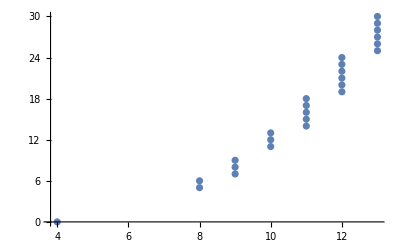

```mathematica
ListPlot[values]
```

```mathematica
Show[{ListPlot[values],Plot[-22.853591160221143+3.68508287292819 x,{x,10}]}]
```

Plot::pllim: Range specification {x,10} is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in Show[{,Plot[-22.8536+3.68508 x,{x,10}]}].

Show[{-Graphics-,Plot[-22.8536+3.68508 x,{x,10}]}]

```mathematica
FindFormula[values]
```

-22.8536+3.68508 #1&

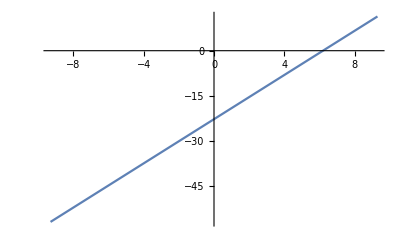

```mathematica
Plot[(-22.853591160221143+3.68508287292819 #1&)[x],{x,-9.302473763118467,9.302473763118467}]
```